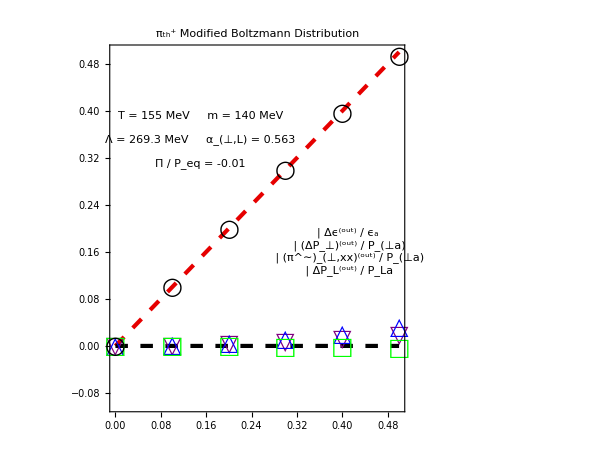

```mathematica
(*ANISOTROPIC PION BOLTZMANN GAS*)

T0 = 0.155;
mass = 0.140;  (* pion mass scale *)
sign = 0;
αT = 0.5;
αL = 0.5;
Λ = 0.3025; (* GeV *)
frac=Table[0.1*i,{i,0,5}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,0.000710089,0.00284172,0.00639896,0.0113886,0.0178204};

ΔPToverPTdata = {0.0,0.00126343,0.00505821,0.011398,0.0203057,0.0318143};

ΔPLoverPLdata = {0.0,-0.000143292,-0.000576286,-0.00130843,-0.00235572,-0.0037412};

piperpoverPTdata = {0.0,0.0999443,0.199554,0.298492,0.396417,0.49298};

style={Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{EdgeForm[Directive[Thick,Purple]],White,Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->16],Style["Δϵ^(out) / ϵ_a",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Blue]],White,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->16],Style["(ΔP_⊥)^(out) / P_(⊥a)",FontSize->14]},
{Graphics[{Directive[Thick,Black],Circle[]},ImageSize->16],Style["(π^∼)_(⊥,xx)^(out) / P_(⊥a)",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->16],Style["ΔP_L^(out) / P_La",FontSize->14]}}],Background->White];

legend2=Panel[Grid[{{Style["T = 155 MeV     m = 140 MeV",FontSize->14]},{},
{Style["Λ = 269.3 MeV     α_(⊥,L) = 0.563",FontSize->14]},{},{Style["Π / P_eq = -0.01",FontSize->14]}}],Background->White];


Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
piperpoverPTplot = Table[{frac[[i]],piperpoverPTdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.1,0.5},ImageSize->600,PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->22},AspectRatio->0.75],
ListPlot[{Δϵoverϵplot,ΔPToverPTplot,ΔPLoverPLplot,piperpoverPTplot},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{▽,24},{△,24},{□,24},{○,24}},PlotStyle->{Purple,Blue,Green,Black},BaseStyle->{FontSize->22},AspectRatio->0.75]}
},Epilog->{Inset[legend1,{0.41,0.16}],Inset[legend2,{0.15,0.35}]},ImageSize->{600,600},FrameLabel->{"(π^∼)_(⊥,xx)^(in) / P_(⊥a)"},PlotLabel->Style["π_th^+ Modified Boltzmann Distribution",FontSize->22]]
```